# Acceptance-Rejection Method

## Example 1: Exponential Distribution

## SCIMATH202 Project: Spring 2021 University College Roosevelt Robin van den Berg

```mathematica
ClearAll[Evaluate[Context[]<>"*"]]
(* This line clears all variables previously defined by the user. *)
```

```mathematica
n=50000
(* This defines our sample size for the simulation (N). *)
```

50000

```mathematica
c=8
(* This defines the value of "c" for the simulation that we calculated in the project report. *)
```

8

```mathematica
data=Table[,{n}];
(* This creates a table to store our data, called "data." *)
```

```mathematica
Do[
mylist={};
u=RandomVariate[UniformDistribution[{0,1}]] ;
y=RandomVariate[UniformDistribution[{0,8}]];
pair={u,y};
AppendTo[mylist,pair];
data[[ii]]=mylist;
,{ii,1,n}]
(* This takes one observation from the Uniform Distribution (0, 1) (our u) and one observation from the Uniform Distribution (0, 8) (our y) and stores them as a pair in the table "data." It repeats this process "n" times . *)
```

```mathematica
Flatten[data,1];
(* This alters the format of the table so that it is suitable for graphing. *)
```

```mathematica
f[x_]:=ⅇ^-x;
(* This defines the target distribution f(x) from which we want to sample. *)
```

```mathematica
g[x_]:= 1/(8-0);
(* This defines the proposal distribution g(x). *)
(* This is also the distribution follwoed by Y. *)
```

```mathematica
accept=Cases[data,{{u_,y_}}/; u≤f[y]/(c*g[y]) ];
(* This defines our acceptance rejection rule for this simulation. For each pair of obervations in "data" the first observation is called u and the second observation is called g. Our acceptance rejection rule is to accept the y observations where u < f[y]/c*g[y]. *)
```

```mathematica
acceptedUY =Flatten[accept,1];
(* This alters the format of the list of accepted pairs so that it is suitable for graphing. It also stores the pairs as a new variable. *)
```

```mathematica
acceptedY = acceptedUY[[All,2]];
(* This creates a new variable that only keeps the the y in every pair that has been accepted. *)
```

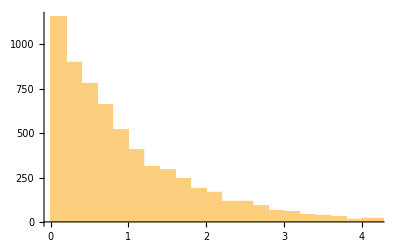

```mathematica
Histogram[acceptedY]
```

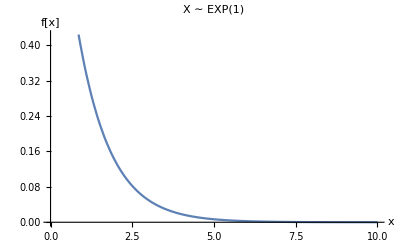

```mathematica
Plot[f[x],{x,0,10},PlotLabel->"X ∼ EXP(1)",AxesLabel->{"x","f[x]"}]
```

```mathematica
p1=Histogram[acceptedY,{0,8,0.5},"Probability"];
p2=Plot[1/2 f[x],{x,0,8}];
```

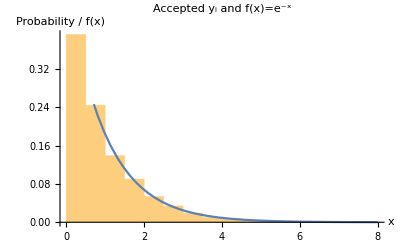

```mathematica
Show[p1,p2,PlotLabel-> "Accepted y_i and f(x)=e^-x", AxesLabel-> {"x", "Probability / f(x)"}, PlotLegends-> {"f(x)"}]
(* This plots our accepted y against the pdf of an exponential distribution with a rate parameter of 1 to ensure that the accpted y follow the desired distribution. *)
```

```mathematica
Export["ARM1",%1035,"JPEG"]
```

ARM1

```mathematica
"ARM1"
```

ARM1